# Ringdown Fitting and Data Analysis

## Overview

The merger of two black holes, or any sufficiently massive compact objects, will result in a highly perturbed black hole which will ring down through the emission of gravitational waves.  The KerrRingdown` Paclet provides an extensible structure for analyzing the gravitational-wave ring-down signal by fitting the signal to the Quasinormal Modes (QNMs) of the Kerr geometry.  The Paclet currently provides routines to read in gravitational-wave data sets from the SXS collaboration, but support for other collections of gravitational-wave data sets can be easily added.  An extensive set of tabulated spin-weight -2 QNMs, available from the Zenodo repository https://doi.org/10.5281/zenodo.14024959,  can be used as the basis for the ring-down fitting.  These QNM data sets were computed using the publicly available KerrModes` suite of Paclets based on the approach developed by Cook and Zalutskiy (2014).  The ring-down fitting methods used in this Paclet were developed by Cook (2020) and Gao and Cook (2024).

The KerrRingdown` Paclet assumes that the gravitational-wave signal ψ_NR is represented as a set of spin-weight -2 harmonic mode functions C_ℓm(t)  via

ψ_NR=∑_ℓm C_ℓm(t)_-2 Y_ℓm(θ,ϕ)≡∑_ℓm C_ℓm(t)ℓm,

where t is a retarded time coordinate.  The notation ℓm is shorthand Dirac braket notation for functions spanning the {θ,ϕ} space.  In this case,  ℓm represents the spin-weight -2 spherical harmonics _-2 Y_ℓm(θ,ϕ).

The ring-down fitting function ψ_fit can be written compactly as

ψ_fit=∑_k C_k ψ_k,

where each ψ_k is a specific QNM defined by

ψ_k=e^(-ⅈ ω_k t)_-2 S_ℓm(θ,ϕ;aω_k)≡e^(-ⅈ ω_k t)k

_-2 S_ℓm(θ,ϕ;aω_k) are the spin-weight -2 spheroidal harmonics, and ω_k is a specific complex QNM frequency.  The QNM index k is compact notation referring to a specific QNM with harmonic indices ℓ and m, overtone index n, and chosen from one of the two families of mode frequencies ω_ℓmn^+(a) and ω_ℓmn^-(a).  So, k is shorthand for a specific ℓmn± which represents the spin-weight -2 spheroidal harmonics _-2 S_ℓm(θ,ϕ;aω_ℓmn^±). Also, a is the usual Kerr rotation parameter a=J_f/M_f, where J_f is the angular momentum of the remnant black hole and M_f is its mass.

### Linear Fitting

In situations where the physical properties of the remnant black hole are know, then finding the QNM expansion coefficients reduces to a simple linear problem.  The physical parameters of the remnant black hole are its mass M_f and angular momentum vector  OverVector[J_f].  We assume that gravitational-wave data is provided in the rest frame of the remnant black hole.  Violating this assumption will cause velocity dependent mode mixing between the different QNMs.

### The Eigenvalue Method

The QNM expansion coefficients C_k in the fit function can be determined in a few different ways.  The default method is the Eigenvalue Method which extremizes the overlap of the signal and the fitting function, where the overlap ρ is define by

ρ^2=(|⟨ψ_fit|ψ_NR⟩|)^2/(⟨ψ_NR|ψ_NR⟩⟨ψ_fit|ψ_fit⟩),

and the inner product between any two complex functions is defined as

⟨ψ_1|ψ_2⟩=∫_t_i^t_e ∮ψ_1^*(t,Ω)ψ_2(t,Ω)ⅆΩⅆt.

Given a specific ordering of the QNMs used in a given fitting function, and with the QNM index indicating that ordering, then we can define a source vector A⃗ and a mode matrix 𝔹 whose components are defined by

A_k≡ψ_kψ_NR and B_ij≡ψ_iψ_j,

Then the QNM expansion coefficients C_k are the components of the vector C⃗=𝔹^-1·A⃗.

which yields the maximum overlap

ρ_max^2=1/⟨ψ_NR|ψ_NR⟩(A⃗)^†·𝔹^-1·A⃗=((|(C⃗)^†·A⃗|)^2)/(⟨ψ_NR|ψ_NR⟩(C⃗)^†·𝔹·C⃗).

The inverse of the mode matrix 𝔹 is obtained as the pseudo-inverse using singular-value decomposition.  For the pseudo-inverse, the reciprocals of any vanishing singular values are replaces with zero when the inverse is constructed.

### Linear Least Squares

The QNM expansion coefficients C_k in the fit function can also be determined by standard linear least squares fitting methods.  In this case, an equation of the form

∑_k e^(-ⅈ ω_k t)ℓ mk C_k=C_ℓm(t)

exists for each value of t in the simulation data being fit for each simulation modeC_ℓm(t).  The full set of equations can be expressed in matrix notation as

𝕃·C⃗=R⃗,

where 𝕃 is the Design Matrix for the linear fitting problem.  This set of equation can be solve directly using singular value decomposition, or it can be rewritten as the normal equation

(𝕃^†·𝕃)·C⃗=𝕃^†·R⃗,

where (𝕃^†·𝕃) is the Normal Matrix for the linear fitting problem.  This set of equation can be solve directly using singular value decomposition.

### Relation between the Eigenvalue Method and Linear Least Squares

The mode matrix 𝔹 is similar to the Normal matrix (𝕃^†·𝕃), but they are not identical, and the two fitting approaches do not yield identical results.  There are two key differences.  One is that the components of 𝔹 are construct from integrals over time, while the components of  (𝕃^†·𝕃) result from discrete sums over time.  More importantly, the angular integrals in 𝕃 are all of the form ℓ mk meaning that they never sample the angular behavior of the QNMs outside of the space spanned by the spin-weight -2 spherical harmonics included in the signal.  A similar behavior can be imposed on the mode matrix 𝔹 if we define a new, mode limited fit function (ψ̃)_fit as

(ψ̃)_fit=∑_ℓm ℓmℓm ψ_fit≡∑_k C_k(ψ̃)_k.

We see that A_k=ψ_kψ_NR=(ψ̃)_kψ_NR is unchanged, but we find that 𝔹_ml≠𝔹 where

(B_ml)_ij≡(ψ̃)_i(ψ̃)_j.

We see, then, that it is 𝔹_ml which is most similar to (𝕃^†·𝕃).  And if we construct the QNM expansion coefficients from C⃗=𝔹_ml^-1·A⃗, then the fitting result are nearly identical to those from linear least squares up to the small differences associated with integration versus summation over time.

### Non-Linear Fitting

In situations where the physical properties of the remnant black hole are either not known, or we wish to ignore their known values, then finding the fitting function also includes determining values for these physical parameters.  This process is inherently nonlinear because the QNM frequences ω_ℓmn^±(a) depend on these parameters.  While the full set of physical parameters is 4-dimensional, we can only determine a 3-dimensional subset of these parameters.  In terms of dimensionless variables, these three parameters are:

δ=M_f/M  :  the mass ratio where M is the natural mass scale used in the simulation data.
χ_f=(|(J⃗)_f|)/M_f^2  :  the dimensionless spin magnitude.
β  :  the angle between the z-axis of the frame used to define the gravitatinal wave data and the direction of OverVector[J_f].

The fourth parameter α corresponds to the angle of rotation of  OverVector[J_f] about the z-axis, however this parameter is degenerate with an overall complex phase in the fitting function and cannot be determined.  Consequently, non-linear fitting corresponds to extremizing the overlap ρ over a 3-dimensional parameter space of (δ,χ_f,β) where evaluation of ρ at each point in the parameter space involves solving the linear fitting problem with specified physical parameters.  Fortunately, in many situations, the gravitational-wave data can be pre-processed to ensure that the data corresponds to be extracted in the rest frame of the remnant black holes and is aligned so that β=0, thus reducing the fitting space to 2 dimensions.

## Read in Numerical Relativity Waveforms

ReadWaveforms[directory,  {{l_1, m_1},{l_2, m_2},...}, DataType →Type] | Read in signal modes {l,m} from waveform file in the specified directory .  Additional options are required depending on the specific data-file format.

Read in gravitational-wave signals.

The function ReadWaveforms reads in gravitational-wave signals from Numerical Relativity (NR) simulations and provides the signal data in the form of a set of harmonic-mode time series data C_ℓm(t) .

Currently, ReadWaveforms supports reading in locally stored data from the SXS Catalog, and supports the data sets where the waveform is computed using the original extrapolation method and also the more accurate Cauchy-Characteristic Extraction (CCE) method.  It is intended that ReadWaveforms be extensible so that data from additional waveform catalogs can be included.

Two reduced data sets from the SXS Catalog are included within the KerrRingdown` Paclet which are used for demonstration purposes.  These correspond to the waveforms SXS:BBH:0305 and SXS:BBH_ExtCCE:0001.

We can read in waveforms from the data sets included with the KerrRingdown` Paclet by specifying the directory as "KerrRingdown".  This only applies to the packaged data sets.  In general, you will need to specify the path to the specific directory containing the data you are interested in.

Read in signal modes {2,2} and {3,2} of the gravitational strain from the included SXS:BBH:0305 data set.

```mathematica
ReadWaveforms["KerrRingdown",{{2,2},{3,2}},
T0->3692.8479955252005,DataType->SXS,WaveformType->Metric,SXSRNext->2,FrameType->CoM,DataRange->All]
```

Read in the same data, but only store the last 1500 data points:

```mathematica
ReadWaveforms["KerrRingdown",{{2,2},{3,2}},
T0->3692.8479955252005,DataType->SXS,WaveformType->Metric,SXSRNext->2,FrameType->CoM,DataRange->{-1500,-1}]
```

Read in signal mode {2,2}  of the gravitational strain from the included SXS:BBH_ExtCCE:0001 data set.

```mathematica
ReadWaveforms["KerrRingdown",{{2,2}},
T0->0,DataType->SXSCCE,WaveformType->Metric,SXSRNext->292,FrameType->CoM,DataRange->All,Superrest->True]
```

When the waveform is loaded, the time-series data is store in the form of a Mathematica List which is addressed by in index.  Determining which element of a list corresponds to a certain time is aided by the  function TimeIndex .

TimeIndex[t] | Find the index for the currently stored time-series data that has a time closest to the specified value of t.

The index of the peak intensity of the waveform (t_peak=0):

```mathematica
TimeIndex[0.0]
```

11

## Plot the NR waveform

PlotClm[l,m] | Returns a list of {t,C_lm} pairs suitable for plotting the full complex time-series data C_ℓm(t). 
PlotReClm[l,m] |  Returns a list of {t,Re[C_lm]} pairs suitable for plotting the Real part of the full complex time-series data Re[C_ℓm(t)]. 
PlotImClm[l,m] |  Returns a list of {t,Im[C_lm]} pairs suitable for plotting the Real part of the full complex time-series data Im[C_ℓm(t)]. 
PlotAbsClm[l,m] | Returns a list of {t,Abs[C_lm]} pairs suitable for plotting the Real part of the full complex time-series data |C_ℓm(t)|. 
PlotSumAbs2Clm[{{l_1,m_1}, {l_2,m_2},...}] | Returns a list of {t, ∑_lm |C_lm|^2} pairs suitable for plotting the Sum of the Square-Magnitudes of the full complex time-series data ∑_ℓm (|C_ℓm(t)|)^2.

Functions can be used to plot the NR waveforms.

After the waveform is read in using ReadWaveforms, use PlotReClm to generate a list of {t,Real[C_lm]} for plotting:

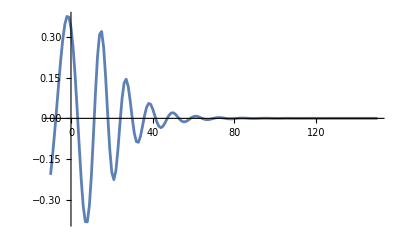

```mathematica
ListLinePlot[PlotReClm[2,2],PlotRange->All]
```

## Remnant Properties of the NR waveform

### SXS Catalog metadata

Properties of the Remnant black hole are stored in the "metadata.txt" file found in each simulation directory:

remnant-mass | The Christodoulou mass M_c of the final black hole  is given by M_c^2=M_irr^2+J^2/(4 M_irr^2), where M_irr is the irrecducable mass of the black hole's horizon. The remnant mass is given as the ratio δ=M_c/m, where m is the natural mass scale used in the simulation.
remnant-dimensionless-spin | The Cartesian components χ_(x,)χ_(y,)χ_z of the dimensionless spin vector χ⃗=(J⃗)/M_c^2.
remnant-velocity | The Cartesian components v_(x,)v_(y,)v_z of the coordinate velocity v⃗ of the remnant black hole's center.

Remnant properties listed in the metadata.txt file.

The ring-down fitting routines need the remnant properties of the final black hole in the rest frame of the remnant black hole.  These properties are the mass ratio δ, the magnitude of the dimensionless spin parameter χ, and the direction of the black hole's angular momentum relative to the extraction coordinate system (θ,ϕ).  These quantities are returned by SXSFinalProperties given the SXS remnant parameters.

SXSFinalProperties[δ, χ_x, χ_y, χ_z, v_x, v_y, v_z] | gives the remnant Black Hole properties {δ, χ, θ, ϕ} based on the given  information from the simulation

Calculate the remnant Black Hole properties {δ, χ, θ, ϕ}.

Using the information in "metadata.txt" from the included SXS:BBH:0305 data set:

```mathematica
BHProperties=SXSFinalProperties[0.952032939704, 5.25395868351*10^(-8),-2.45673365593*10^(-08), 0.692085186818, -0.000297055913076, -0.000334747685807, -2.23049871826*10^(-8)]
```

{0.952033,0.692085,8.38028×10^-8,-0.437448}

It is important to note that if the coordinate velocity of the remnant black hole is not very small (ideally zero), then mode mixing will occur and the ring-down fitting routines will not return reliable results.  The SXSFinalProperties routine performs a relativistic transformation of the remnant parameters to return results as measured in the rest frame of the final black hole, where the coordinate velocity v⃗ defines the relative velocity of the final black hole relative to the frame in which the SXS remnant parameters are measured.  So long as the coordinate velocity is small, SXSFinalProperties  will simply return the input parameters with the dimensionless spin expressed in terms of its magnitude and direction.

If the coordinate velocity is not small, then the spin of the black hole is transformed as if it were associated with a point particle using the proper relativistic transformation OverVector[J']=γ(J⃗-γ/(γ+1)v⃗(v⃗·J⃗)) where γ=1/(√(1-v^2)) is the usual Lorentz factor and we assume the particle is passing through the origin so that there is no orbital angular momentum.  In addition to a relativistic correction to the black hole's angular momentum, there will also be a change in its rest mass.  That is, the mass ratio will transform to δ'=δ/γ_χ where γ_χ is a relativistic correction factor due to the frame dependance of the black hole's angular momentum.  This can be fixed by using the fact that the irreducible mass of an isolated black hole is frame/slicing independent.  From this, it directly follows that γ_χ^2=(M_c/M_c')^2=(1+√(1-χ'^2))/(1+√(1-χ^2)) where χ'^2=γ^2 γ_χ^4[χ^2-(v⃗·χ⃗)^2].  Together, these can be solved to yield γ_χ^-2=1/2[1+√(1-χ^2)+γ^2(χ^2-(v⃗·χ⃗)^2)/(1+√(1-χ^2))].  The final result is that OverVector[χ']=γγ_χ^2(χ⃗-γ/(γ+1)v⃗(v⃗·χ⃗)).

Note that SXSFinalProperties does not transform the associated signal data to the rest frame of the final black hole.  For best results, ring-down data should be transformed to the superrest frame using BMS transformations.  If the remnant properties returned by SXSFinalProperties do not agree with the input data, then the ring-down data is not in the rest frame and ring-down fitting results should not be trusted.

## Read in QNM data

HDF5QNMDir[directory] | Set the directory storing  the HDF5 data files which contain the Quasinormal Mode data files.

Set up the QNM data directory.

Set the QuasiNormal Mode(QNM) data directory:

```mathematica
HDF5QNMDir["KerrRingdown/"]
```

KerrRingdown/

The data files in the specified directory are named KerrQNMTable_nn.h5, where nn is a 2-digit integer representing the overtone associated with all of the data stored in the file.  The full set of data files can be downloaded from the  Zenodo repository https://doi.org/10.5281/zenodo.14024959.

The QNM data files contain the QNM frequence ω_ℓmn(a), the angular separation constant _-2 A_ℓm(aω_ℓmn), and the spheroidal expansion coefficients _-2 𝒜_(ℓ̂ ℓm)(aω_ℓmn) at specific values of a.  Cubic interpolation is used to obtain the data at any required value of a in the range 0≤a≤1.

A small subset of the compete set of data files are contained within the KerrRindown` Paclet.  This data can be accessed by setting the directory to "KerrRingdown/".

## Linear Fitting with OverlapFit

The OverlapFit function within KerrRingdown` is the key function for performing ring-down fitting.  In its normal operation, a single fit extremizes the overlap ρ defined by

ρ^2=(|⟨ψ_fit|ψ_NR⟩|)^2/(⟨ψ_NR|ψ_NR⟩⟨ψ_fit|ψ_fit⟩),

where the inner products are evaluated by

⟨ψ_1|ψ_2⟩=∫_t_i^t_e ∮ψ_1^*(t,Ω)ψ_2(t,Ω)ⅆΩⅆt.

The upper limit of integration is fixed by the option TEnd which is set to a specific index into the list of simulation times.  The lower limit of integration typically takes on a sequence of values t_0≤t_i≤t_f leading to sequence of fits with each performed at a different start time t_i.  The specific values of t_i are taken from the list of simulation times with the option T0 setting the index of the time t_0, and the option TFinal setting the index of the time t_f.  Normally, fits for all simulation times in the range t_0≤t_i≤t_f  are computed, however, the FitTimeStride option can be used to modify this.

The gravitational-wave signal which is being fit ψ_NR is given by

ψ_NR=∑_ℓm C_ℓm(t)_-2 Y_ℓm(θ,ϕ),

with the data taken from the data set imported into Mathematica during the most recent call to ReadWaveforms.   The specific set of signal modes C_ℓm(t) used to represent ψ_NR is specified by the SimModes argument to OverlapFit.

The fitting function ψ_fit is a linear combination of QNMs given by

ψ_fit=∑_k C_k ψ_k,

where each ψ_k is a specific QNM defined by

ψ_k=e^(-ⅈ ω_k t)_-2 S_ℓm(θ,ϕ;aω_k),

Data for the QNMs is read from HDF5 files stored in a directory specified by calling HDF5QNMDir.  Two families of QNMs exist and are referenced as ω_ℓmn^+(χ) and ω_ℓmn^-(χ), where to two families are related by ω_ℓmn^-=-(ω_(ℓ(-m)n)^+)^*.  Only data for the  ω_ℓmn^+(χ) family are stored in the HDF5 files since all of the data for the ω_ℓmn^-(χ) family can be generated from them.   However, when specifying a specific fitting model ψ_fit, the set of ω_ℓmn^+(χ) modes is specified by the QNModesp argument to OverlapFit while the ω_ℓmn^-(χ) modes are specified by the QNModesm argument.

The assumed properties of the remnant black hole are expressed as the list {δ, χ, θ, ϕ} given as the BHproperties argument to OverlapFit.  For linear fitting, these properties are taken as known quantities and can be obtained from SXS metadata files by using the SXSFinalProperties function.

OverlapFit[BHproperties, SimModes, QNModesp, QNModesm] | Returns a list containing all of the linear-fit information for each fit in the specified time range.  This information incudes the start time of each fit, and at each time gives the overlap, fit amplitues, fit errors, the black-hole properties, and the lists of all simulation and QNM modes used in the fits.
SXSFinalProperties[δ, χ_x, χ_y, χ_z, v_x, v_y, v_z] | Can be used to create the list of black-hole remnant properties for BHproperties.
SimulationModes[l,m] | Can be used to create a list of SimModes.
QNModes[l,m,n] |  Can be used to create lists of QNMs for QNModesp and QNModesm

OverlapFit is used to find a time series of linear fits.

Set the QuasiNormal Mode(QNM) data directory.  Read in signal modes {2,2} and {3,2} of the gravitational strain  and set the black-hole properties from the data in the SXS metadata file, all from the included SXS:BBH:0305 data set:

```mathematica
HDF5QNMDir["KerrRingdown/"];
```

```mathematica
ReadWaveforms["KerrRingdown",{{2,2},{3,2}},T0->3692.8479955252005,DataType->SXS,WaveformType->Metric,SXSRNext->2,FrameType->CoM,DataRange->All];
```

```mathematica
BHProperties=SXSFinalProperties[0.952032939704, 5.25395868351*10^(-8),-2.45673365593*10^(-08), 0.692085186818, -0.000297055913076, -0.000334747685807, -2.23049871826*10^(-8)];
```

The options passed to OverlapFit can be passed in the function call, or desirable default values can be preset using SetOptions.  In this example, default values for the T0, TFinal, and TEnd options are set so that T0 corresponds to the index closest to t=0, TFinal to the index closest to t=50m, and TEnd to the index closest to t=90m.

```mathematica
SetOptions[OverlapFit,T0->TimeIndex[0],TFinal->TimeIndex[50],TEnd->TimeIndex[90]]
```

{FitTimeStride→False,PhaseChoice→SL-C,RescaleModes→False,RestrictToSimulationSubspace→False,ReturnSingularValues→False,SVDWorkingPrecision→MachinePrecision,T0→109,TEnd→1009,TFinal→609,Tolerance→0,UseLeastSquares→False}

Use only the C_22(t) simulation mode for the fit :

```mathematica
simModes=SimulationModes[2,2]
```

{{2,2}}

Use the ω_220^+ and  ω_320^+ QNMs for the fit function:

```mathematica
qnmp=QNModes[Range[2,3],2,0]
```

{{2,2,0},{3,2,0}}

Fit the QNMs to the simulation modes for start times 0≤t_i≤50m :

```mathematica
overlapFitResult=OverlapFit[BHProperties,simModes,qnmp,{}];
```

By default, OverlapFit performs fitting using the Eigenvalue method.  However, fits can be performed using linear least-squares fitting by setting the UseLeastSquares option to either DesignMatrix or NormalEquation.  When linear least-squares fitting is performed, instead of maximizing the overlap, the mean-square deviation χ_ls^2 is minimized, where

χ_ls^2=∑_(t,{NR}) (|ψ_NR-∑_k C_k(ψ̃)_k|)^2,

and the first sum is over all values of t over which the fit is being performed and for each simulation mode in the set of modes representing the signal.  Notice that the fit function is composed from the mode-limited QNMs (ψ̃)_k.

The Eigenvalue method can also produce a fit which is nearly the same as a linear least-squares fit if the we set the option RestrictToSimulationSubspace→True   When this option is set, the overlap is computed using the mode-limited fitting function (ψ̃)_fit in place of the full fitting function, and it is this overlap which is maximized.

## Analyze the OverlapFit Result

### Mismatch

When a waveform is fit to a set of QNMs, the overlap ρ between the ring-down waveform and the fitting function is maximized when the Eigenvalue method is used.  If linear least-squares fitting is used, then it is the mean-square deviation χ_ls^2 which is minimized.  But, in either case, the mismatch ℳ≡1-ρ represents a measure of the quality of the fit.

The overlap ρ is the second element of the OverlapFit output. We can plot the mismatch ℳ as a function of initial fitting time:

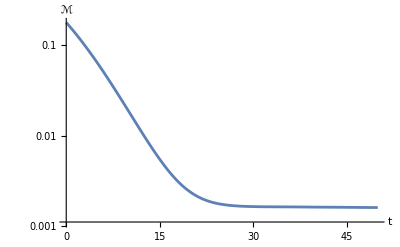

```mathematica
t=overlapFitResult[[1]];
ρ=overlapFitResult[[2]];
ListLogPlot[Transpose[{t,1-ρ}],AxesLabel->{"t","ℳ"},Joined->True]
```

However, there are two ways in which the overlap can be computed.  One is naturally associated with the Eigenvalue method and the other with linear least-squares fitting.  It is important to recognize that comparisons between these two types of overlap are not meaningful.

The spin-weighted spheroidal harmonics can be expressed as a linear combination of spin-weighted spherical harmonics:

_s S_ℓm(θ,ϕ;c)=∑_(ℓ̂) _s 𝒜_(ℓ̂ ℓm)(c)_s Y_(ℓ̂ m)(θ,ϕ).

So, the angular space spanned by _s S_ℓm(θ,ϕ;c) typically spans a larger angular space than the related spherical harmonic _s Y_ℓm(θ,ϕ).  When the overlap ρ is computed,

ρ^2=(|⟨ψ_fit|ψ_NR⟩|)^2/(⟨ψ_NR|ψ_NR⟩⟨ψ_fit|ψ_fit⟩),

the inner product ⟨ψ_fit|ψ_fit⟩ can be evaluated in two different ways.  By default, it is evaluated using the full fitting function, but if the option RestrictToSimulationSubspace→True then the mode-limited fit function is used ⟨(ψ̃)_fit|(ψ̃)_fit⟩.  For a given set of QNM expansion coefficients C_k, it will aways be true that ⟨ψ_fit|ψ_fit⟩≥ ⟨(ψ̃)_fit|(ψ̃)_fit⟩.  Thus, the mode-limited overlap will always be larger than the full overlap, and thus the mode-limited mismatch will always be smaller than the full overlap for the same fit.

Because the  RestrictToSimulationSubspace option to OverlapFit affects both the computation of the overlap ρ  and the values of the QNM expansion coefficients C_k when the Eigenvalue method of fitting is used, another function is needed if we wish to evaluate the overlap independently of the fit.   The function RestrictOverlap can be used to recompute the overlap from a prior fit.  RestrictOverlap accepts all of the options from OverlapFit, but its primary purpose is to recomputed the overlap based on the options RestrictToSimulationSubspace and OmitModes.

RestrictOverlap[fit] | gives the recomputed overlap as a list {t, ρ}, using OverlapFit output fit

Compute the mode-limited overlap and compare it to the normal overlap:

```mathematica
overlapML=RestrictOverlap[overlapFitResult,T0->TimeIndex[0],TFinal->TimeIndex[50],TEnd->TimeIndex[90],RestrictToSimulationSubspace->True];
```

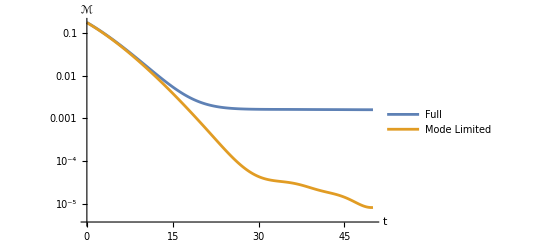

```mathematica
ρML=overlapML[[2]];
ListLogPlot[{Transpose[{t,1-ρ}],Transpose[{t,1-ρML}]},AxesLabel->{"t","ℳ"},Joined->True,PlotLegends->Placed[LineLegend[{"Full","Mode Limited"}],{0.7,0.8}]]
```

### QNM amplitudes and phases

The fitting function can be written as linear combination of QNMs

ψ_fit=∑_(k∈{QNM}) C_k(ⅇ^(-iω_k(t-t_peak)))_-2 S_ℓm(θ,ϕ;𝒶ω_k)

where t_peak is the peak of the simulation waveform.

At different initial fitting time t_i, we can fit C_k as a function of t_i. We can express C_k(t_i) in terms of amplitude and phase, C_k=A_k ⅇ^iϕ_k. The function OverlapSequenceAmplitudes can return the QNM amplitude and phase data from an OverlapFit output.

FitAmplitudesTable[fit, t_i] | Creates  table of amplitudes and phases, and their standard errors, for each QNM mode at the specified fit-start time t_i.
OverlapSequenceCoefPlus[fit,{l,m,n}] | Returns the time sequence of the complex QNM expansion coefficient C_lmn^+(t)  from an OverlapFit result fit.
OverlapSequenceCoefMinus[fit,{l,m,n}] | Returns the time sequence of the complex QNM expansion coefficient C_lmn^-(t)  from an OverlapFit result fit.
OverlapSequenceAmplitudes[fit] | Returns the QNM expansion coefficients and their standard errors for each mode from an OverlapFit result fit. The results are presented as amplitudes and phases.

Create a table of the amplitudes and phases with their uncertainties for all QNMs at t_i=30m:

```mathematica
FitAmplitudesTable[overlapFitResult,30.0]
```

Mode | Amplitude | Phase/π | σ(Amp) | σ(Phase)/π
{2, 2, 0}+ | 0.954304 | 0.178049 | 0.000272556 | 0.0000909114
{3, 2, 0}+ | 0.0445538 | -0.299954 | 0.000309815 | 0.00221346

Extract the time and C_220^+ coefficient data:

```mathematica
t=overlapFitResult[[1]];
C220=OverlapSequenceCoefPlus[overlapFitResult,{2,2,0}];
```

Plot the amplitude and phase of C_220^+ :

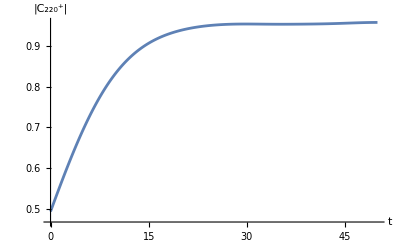

```mathematica
ListLinePlot[Transpose[{t,Abs[C220]}],AxesLabel->{"t","|C_220^+|"}]
```

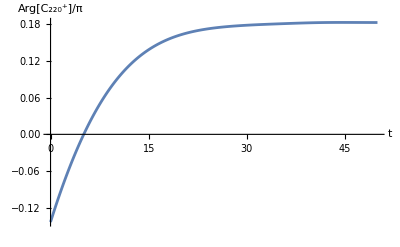

```mathematica
ListLinePlot[Transpose[{t,Arg[C220]/π}],AxesLabel->{"t","Arg[C_220^+]/π"}]
```

Extract the time, QNM expansion coefficients, and their standard errors for all QNMs in the fit.

```mathematica
{t,amps,errors}=OverlapSequenceAmplitudes[overlapFitResult];
```

```mathematica
qnmplist=overlapFitResult[[4,3]];
qnmmlist=overlapFitResult[[4,4]];
index220=QNMpIndex[qnmplist,qnmmlist,{2,2,0}];
index320=QNMpIndex[qnmplist,qnmmlist,{3,2,0}];
```

```mathematica
Amp220=Flatten[Take[amps,{index220},All,{1}]];
Phase220=Flatten[Take[amps,{index220},All,{2}]];
Amp320=Flatten[Take[amps,{index320},All,{1}]];
Phase320=Flatten[Take[amps,{index320},All,{2}]];
```

```mathematica
ErrAmp220=Flatten[Take[errors,{index220},All,{1}]];
ErrPhase220=Flatten[Take[errors,{index220},All,{2}]];
ErrAmp320=Flatten[Take[errors,{index320},All,{1}]];
ErrPhase320=Flatten[Take[errors,{index320},All,{2}]];
```

Plot the amplitudes and phases for C_220^+ and C_320^+ , including error bars for every 20^th data point.

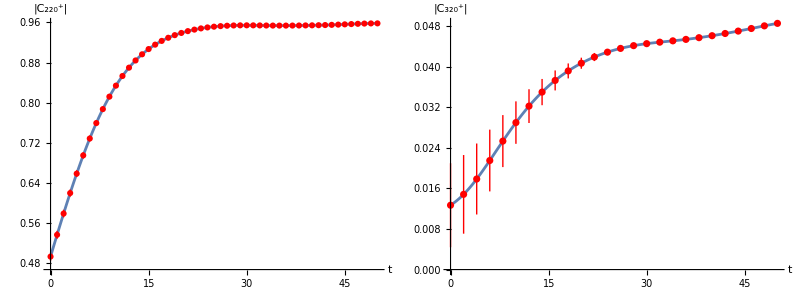

```mathematica
Grid[{{Show[ListLinePlot[Transpose[{t,Amp220}],AxesLabel->{"t","|C_220^+|"},ImageSize->Scaled[0.4]],ListPlot[Take[Transpose[{t,Around[#[[1]],#[[2]]]&/@Transpose[{Amp220,ErrAmp220}]}],{1,-1,10}],PlotStyle->Red]],Show[ListLinePlot[Transpose[{t,Amp320}],AxesLabel->{"t","|C_320^+|"},ImageSize->Scaled[0.4]],ListPlot[Take[Transpose[{t,Around[#[[1]],#[[2]]]&/@Transpose[{Amp320,ErrAmp320}]}],{1,-1,20}],PlotStyle->Red]]}}]
```

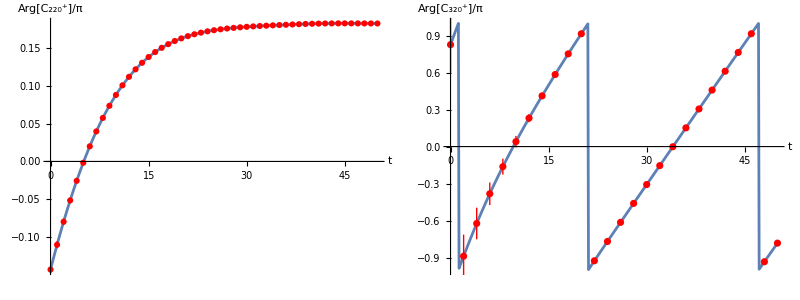

```mathematica
Grid[{{Show[ListLinePlot[Transpose[{t,Phase220}],AxesLabel->{"t","Arg[C_220^+]/π"},ImageSize->Scaled[0.4]],ListPlot[Take[Transpose[{t,Around[#[[1]],#[[2]]]&/@Transpose[{Phase220,ErrPhase220}]}],{1,-1,10}],PlotStyle->Red]],Show[ListLinePlot[Transpose[{t,Phase320}],AxesLabel->{"t","Arg[C_320^+]/π"},ImageSize->Scaled[0.4]],ListPlot[Take[Transpose[{t,Around[#[[1]],#[[2]]]&/@Transpose[{Phase320,ErrPhase320}]}],{1,-1,20}],PlotStyle->Red]]}}]
```

RelativeAmplitudes[fit,{l_s,m_s},t_i] | Return the relative amplitudes contributing to signal mode C_(l_s m_s) based on the the fitted coefficients at time t_i.

Another useful quantity to represent the QNM amplitude information is relative amplitude.   The relative amplitude of the QNM with expansion coefficient C_ℓmn^± contributing to signal mode C_(ℓ_s m_s) is denoted  ℛ_(ℓ_s m_s)C_ℓmn^± and is defined by:

ℛ_(ℓ_s m_s)C_ℓmn^±≡|𝔇_(m_s m)^ℓ_s(0,θ,ϕ)_-2 𝒜_(ℓ_s ℓm)(aω_ℓmn^±)C_ℓmn^±(t_i)|ⅇ^(Im(ω_ℓmn^±t)).

Here:  𝔇_(m_s m)^ℓ_s(0,θ,ϕ) is the Wigner D-function WignerD[{l_s,-m_s,-m},0,θ,ϕ] needed when the rotation axis of the black hole does not align with the z-axis of the simulation coordinates; _-2 𝒜_(ℓ_s ℓm)(aω_ℓmn^±) is a spheroidal expansion coefficient; and C_ℓmn^±(t) is a QNM expansion coefficient.  The fit time t_i can be set to either a specific simulation fit time, or continuous relative amplitudes can be plotted by setting t_i to All.

Obtain the relative amplitude contributing to the Numerical Relativity modes C_22 using function RelativeAmplitudes:

```mathematica
relAmps=RelativeAmplitudes[overlapFitResult,{2,2},All];
R22C220=relAmps[[index220]];
R22C320=relAmps[[index320]];
```

Plot the relative amplitude ℛ_22 C_220^+ as a function of t_i:

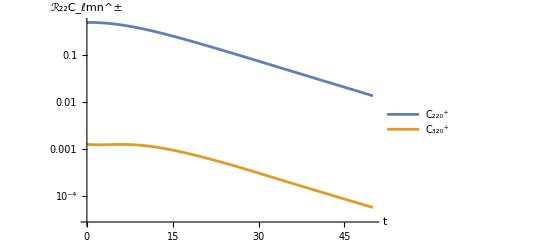

```mathematica
ListLogPlot[{Transpose[{t,R22C220}],Transpose[{t,R22C320}]},Joined->True,PlotLegends->{"C_220^+","C_320^+"},AxesLabel->{"t","ℛ_22C_ℓmn^±"}]
```

### Compare the fitted waveform with the NR waveform

FitMode[fit,{l_s,m_s},t_i] | This function uses the output fit from OverlapFit to reconstruct the GW waveform corresponding to signal mode C_(l_s m_s)(t), based on the QNM expansion coefficients fit at time t_i.

Construct the fitted waveform.

Reproduce simulation mode C_22(t) using the QNM coefficients fitted at t=40M:

```mathematica
fitMode= FitMode[overlapFitResult,{2,2},40];
```

Compare the fitting function with the original signal.  In the plot, the real part is plotted as blue and the imaginary as yellow.  The original signal is plotted as dashed lines, while the output of FitMode is plotted as solid lines.

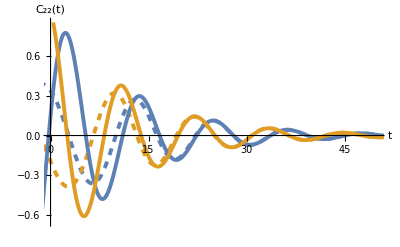

```mathematica
color=Take[ColorData[97,"ColorList"],2];
solid[i_]:=Directive[color[[i]],Thickness[0.007]];
dashed[i_]:=Directive[color[[i]],Thickness[0.007],Dashed];
ListLinePlot[Join[Transpose[{{#[[1]],Re[#[[2]]]},{#[[1]],Im[#[[2]]]}}&/@PlotClm[2,2]],Transpose[{{#[[1]],Re[#[[2]]]},{#[[1]],Im[#[[2]]]}}&/@Transpose[fitMode]]],PlotRange->{{0,50},{-0.65,0.85}},PlotStyle->{dashed[1],dashed[2],solid[1],solid[2]},AxesLabel->{"t","C_22(t)"}]
```

### Other useful functions

QNMpIndex[QNModesp,QNModesm,qnm] | Return the position index of the specified mode C_lmn^+ in the combined lists of QNMs QNModesp and QNModesm.
QNMmIndex[QNModesp,QNModesm,qnm] | Return the position index of the specified mode C_lmn^- in the combined lists of QNMs QNModesp and QNModesm.
SphericalHarmonicModes[{l,m,n},smodes] | Select the subset of signal modes in the list smodes that can overlap with the QNM specified by {l,m,n}.
SpheroidalHarmonicModes[{l,m},qnms] | Select the subset of QNMs in the list qnms that can overlap with the signal mode specified by {l,m}.

A useful application of QNMpIndex and QNMmIndex is to find the position of a specific QNM in results returned by a call to OverlapFit.  The fitting parameters from a given fit are stored in the 4^th element of the return value.  The list of ordinary fit modes QNModesp is the  3^rd element of this list, and the list of mirror fit modes QNModesm is the 4^th element.

The fitting parameters from a given fit are stored in the 4^th element of the return value.  The list of ordinary fit modes QNModesp is the  3^rd element of this list, and the list of mirror fit modes QNModesm is the 4^th element:

```mathematica
fitparams=overlapFitResult[[4]];
qnmplist=fitparams[[3]]
qnmmlist=fitparams[[4]]
```

{{2,2,0},{3,2,0}}

{}

Obtain the position of the ordinary QNM C_320^+:

```mathematica
IndexC320p=QNMpIndex[qnmplist,qnmmlist,{3,2,0}]
```

2

The fit coefficients are stored in the 3^rd element of the fit results, and the time series  C_320^+(t) can be obtained using:

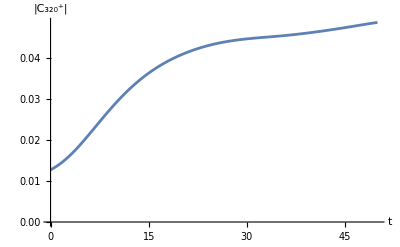

```mathematica
C320=Flatten[Take[overlapFitResult[[3]],All,{IndexC320p}]];
ListLinePlot[Transpose[{t,Abs[C320]}],PlotRange->All,AxesLabel->{"t","|C_320^+|"}]
```

Of course, the same result could have been obtained more easily using OverlapSequenceCoefPlus.

## Nonlinear Fitting: nonlinear optimization in the remnant parameter space

In nonlinear fitting, the remnant black hole's parameters, its mass and spin, are treated as unknown variables along with the QNM expansion coefficients.  Because the the QNMs frequencies ω_ℓmn^± depends on the remnant black hole's parameters, we need to do nonlinear optimization in this parameter space.  This is implemented by maximizing the overlap ρ over the remnant black-hole parameter space.

### Nonlinear Fitting Procedures

RemnantParameterSearch[MassRange,SpinRange,AngleRange,SimModes,QNModesp,QNModesm] | returns a structure containing the results of a set of calls to OverlapFit with varying remnant parameters.  
MaximizeOverlap[δ_g,χ_g,θ_g,t_i,SimModes,QNModesp,QNModesm] | find the optimum remnant parameters near the given parameters at time t_i.
RemnantParameterSpaceMaxOverlap[rps] | finds the maximum overlap, and associated remnant parameters, at a sequence of fit-start times starting from the result rps obtained from RemnantParameterSearch.
RefineMaxOverlapSequence[mos,SimModes,QNModesp,QNModesm] | refines the results mos returned by RemnantParameterSpaceMaxOverlap or RefineMaxOverlapSquence.

Use RemnantParameterSeach to calculate the OverlapFit at each grid point in the parameter space:

```mathematica
rps= RemnantParameterSearch[{0.90,0.98,0.0025},{0.65,0.73,0.0025},0.0,SimulationModes[Range[2,3],2],QNModes[Range[2,3],2,0],{},T0->TimeIndex[30],TFinal->TimeIndex[35],TEnd->TimeIndex[90]];
```

Use RemnantParameterSpaceMaxOverlap to search the optimized mismatch and remnant parameters at each time:

```mathematica
mos= RemnantParameterSpaceMaxOverlap[rps,T0->TimeIndex[30],TFinal->TimeIndex[33],TEnd->TimeIndex[90],FitTimeStride->10];
```

Time Index = 1 : Mismatch = 0.0000244308 δf = 0.95407 χf = 0.692358 θf = 0

Time Index = 2 : Mismatch = 0.0000243269 δf = 0.953792 χf = 0.692361 θf = 0

Time Index = 3 : Mismatch = 0.0000249525 δf = 0.953565 χf = 0.692373 θf = 0

Time Index = 4 : Mismatch = 0.0000259893 δf = 0.953349 χf = 0.692354 θf = 0

RefineMaxOverlapSequence can be used to refine the results from RemnantParameterSpaceMaxOverlap if its results are non-smooth because of noise or poor initial guesses.

### Visualize the RemnantParameterSearch Results

The functions below can help visualizing the results produced by RamnantParameterSearch.

ViewRemnantParameterSpace[rps] | Interactively view  the results from RemnantParameterSearch.
ViewRemnantParameterSpaceδχ[rps,t_i,θ_i] | produces a density plot and determines the parameters of the minimum mismatch found in a 2-dimensional slice of the remnant parameter space produced by RemnantParameterSearch.
AddδχLines[δχplot] | adds lines to a density plot to help visualizing the location of the minimum mismatch.
AddδχLinesandLabel[δχplot,label] | adds lines to a density plot to help visualizing the location of the minimum mismatch, and include a label to display additional information.

View the results by generating a density plot at a specific time:

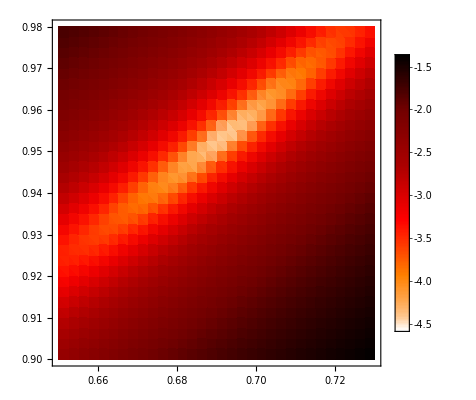
{-Graphics-M_f[M]χ_flog_10ℳ,{0.69,0.9525,-4.5885}}

```mathematica
minMismatch=ViewRemnantParameterSpaceδχ[rps,1,1]
```

Two lines locating the minimum mismatch can be added by using AddδχLines. Any label can be added by using Text["label",{x,y}]. Here we add a label to tell us the position where you have a minimum mismatch:

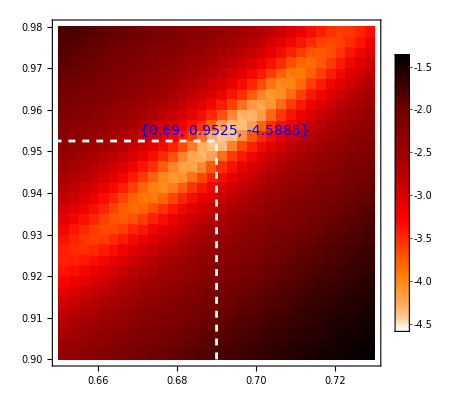
{-Graphics-M_f[M]χ_flog_10ℳ,{0.69,0.9525,-4.5885}}

```mathematica
AddδχLinesandLabel[minMismatch, Text[Style[ToString[minMismatch[[2]]],Blue,14],{0.692,0.955}]]
```

### Analyze the Amplitudes and Phases

MaxOverlapSequenceAmplitudes[mos,SimModes,QNModesp,QNModesm] | computes the OverlapFit using the the black-hole remnant parameter data at every fit-start time in mos.  The QNM expansion coefficients and their standard errors are returns and the results are presented as amplitudes and phases.
MOSAmp[ampdat,index] | returns a list appropriate for plotting QNM amplitudes as a function of time for the QNM specified by index.  The data is taken from ampdat as returned by MaxOverlapSequenceAmplitudes.
MOSPhase[ampdat,index] | returns a list appropriate for plotting scaled QNM phases (ϕ/π) as a function of time for the QNM specified by index.  The data is taken from ampdat as returned by MaxOverlapSequenceAmplitudes.

These functions are used to analyze the amplitudes and phases obtained from nonlinear fitting.

Given the mos obtained in the Nonlinear Fitting Procedures section, we can use MaxOverlapSequenceAmplitudes to obtain the QNM amplitude and phase data:

```mathematica
coefResult=MaxOverlapSequenceAmplitudes[mos,SimulationModes[Range[2,3],2],QNModes[Range[2,3],2,0],{}];
```

Then the amplitude and phase of a specific QNM can be found using MOSAmp and MOSPhase and the index of that QNM:

```mathematica
mosAmp220=MOSAmp[coefResult,1]
mosPhase220=MOSPhase[coefResult,1]
```

{{29.9905,0.952098},{30.9902,0.953103},{31.9898,0.953934},{32.9895,0.954797}}

{{29.9905,0.444817},{30.9902,0.447003},{31.9898,0.448887},{32.9895,0.45052}}

The index of the QNM can be found conveniently by using the functions QNMpIndex and QNMmIndex. In the example before, the QNM index is 1, which corresponds to the QNM (2, 2, 0, +).

### Other useful functions

MergeMaxOverlapSequences[mos_1,mos_2,...] | combines two or more maximum overlap sequences lists mos_i as returned by RemnantParameterSpaceMaxOverlap. The returned list is sorted in time and duplicate time entries are removed.
MergeRPSLists[rps_1,rps_2,...] | combines two or more ring-down parameter search lists rps_i as returned by RemnantParameterSearch. The returned list is sorted in time and duplicate time entries are removed.
MaxOverlapSequenceSVDInfo[mos,SimModes,QNModesp,QNModesm] | recomputes the OverlapFit for each element of mos and prints out the Singular Values.

## Extending the KerrRingdown` Paclet

When KerrRingdown` is loaded, normally the paclet functions are loaded from files in the Kernel subdirectory of the paclet.  However, the paclet has the flexibility to load in alternative versions of the standard paclet functions.

In addition to KerrRingdown.wl, the standard paclet functions found in the Kernel subdirectory are named:

| DataRoutines.wl
       | OverlapFitting.wl
       | QNMModeData.wl
       | ReadWaveforms.wl
       | UtilityRoutines.wl

If any of the following files are located in the paclet subdirectory Local, then they are loaded in place of their counterpart in Kernel:

| DataRoutinesLocal.wl
       | OverlapFittingLocal.wl
       | QNMModeDataLocal.wl
       | ReadWaveformsLocal.wl
       | UtilityRoutinesLocal.wl

This feature can be used create private versions of the paclet fitting routines.

Related Guides

KerrRingdown Function Guide

Related Tech Notes

## Metadata

### Categorization

Tech Note

KerrRingdown

KerrRingdown`

KerrRingdown/tutorial/RingdownFittingAndDataAnalysis

### Keywords

Kerr

Ringdown